```mathematica
data={{0,4},{1,6},{2,8},{3,14},{4,25},{5,40},{6,57},{7,63},{8,87},{9,105},{10,118},{11,153},{12,173},{13,183},{14,188},{15,212},{16,227},{17,265},{18,317},{19,343},{20,361},{21,457},{22,476},{23,523},{24,538},{25,595},{26,685},{27,780},{28,896},{29,1000},{30,1100},{31,1200},{32,1400},{33,1700},{34,2000},{35,2400},{36,2800},{37,3300},{38,4300},{39,5300},{40,6800},{41,8500},{42,10300},{43,12700},{44,14900},{45,17500},{46,21200},{47,25200},{48,29100},{49,32800},{50,37800},{51,44900},{52,47400},{53,63600},{54,75100},{55,81700},{56,100500},{57,116100},{58,133800},{59,161600},{60,190900},{61,223200},{62,254600}};
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

13.1866 ⅇ^(0.159405 t)

(4.16842×10^6)/(1+129.008 ⅇ^(8.04802-0.164288 t))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c[t]→(1. ⅇ^(0.183486 t) k)/(1. ⅇ^(0.183486 t)-0.25 (4.-1. k)^1.)}}

FittedModel[(903827. ⅇ^(«19» t))/(225956.+1. ⅇ^(«19» t))]

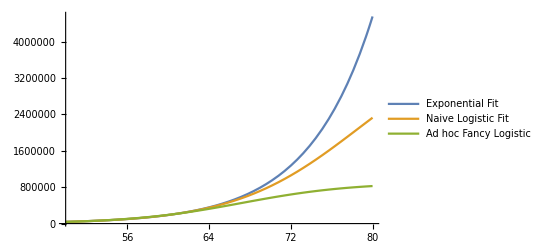

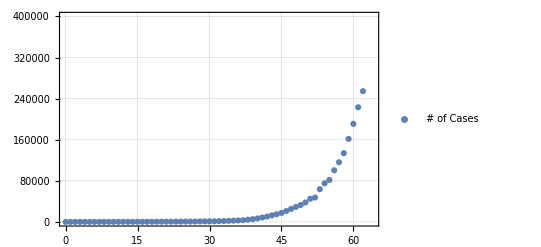

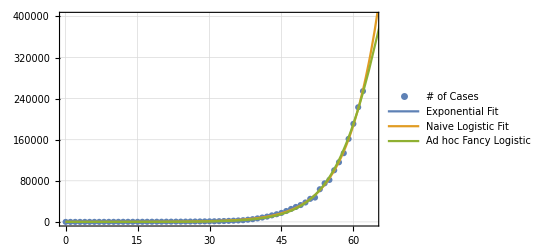

```mathematica
fit=NonlinearModelFit[data,a Exp[-b t],{a,b,c},t];
fit2=NonlinearModelFit[data,c/(1+a*Exp[-b t+d]),{a,b,c,d},t];
Normal[fit]
Normal[fit2]
sol=DSolve[{c'[t]==1/5.45*c[t]*(1-(c[t]/k)),c[0]==4},c[t],t]
fit3=NonlinearModelFit[data,c[t]/.sol,k,t]
Plot[{Normal[fit],Normal[fit2],Normal[fit3]},{t,50,80},PlotRange->All,PlotLegends->{"Exponential Fit","Naive Logistic Fit","Ad hoc Fancy Logistic"}]
scatterPlot=ListPlot[data,PlotRange->{{0,64},{0,400000}},Frame->True,GridLines->Automatic,PlotLegends->{"# of Cases"}]
fitPlots=Plot[{Normal[fit],Normal[fit2],Normal[fit3]},{t,0,1000},PlotRange->All,PlotLegends->{"Exponential Fit","Naive Logistic Fit","Ad hoc Fancy Logistic"}];
Show[scatterPlot,fitPlots]
```